# h=I+A+B

Extrapolation of  the ||M_n|| norms described in the paper
“A COMPUTATIONAL APPROACH TO THE THOMPSON GROUP F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
norms={{1,2.9999999999999996},{2,5.000000000000001},{3,5.999999999999999},{4,6.561552812808831},{5,6.90951596615595},{6,7.141336115655365},{7,7.304337743007365},{8,7.432163237993422},{9,7.531993362930429},{10,7.61434713292474},{11,7.681428519345555},{12,7.73954284784636},{13,7.788108145812049},{14,7.831595176942418},{15,7.868872357791319},{16,7.902753284389529},{17,7.932409830305334},{18,7.959849162636051},{19,7.984180489022279},{20,8.006956664241345},{21,8.027335460419687},{22,8.046597046112455},{23,8.063989225969943},{24,8.080527409475819},{25,8.095647014527733},{26,8.11006079249735},{27,8.123304037527939},{28,8.136018060209928},{29,8.147759937749639},{30,8.159067041231319},{31,8.169564285141952},{32,8.179709741060485},{33,8.189171701328226},{34,8.19833781133207},{35,8.20692641290236},{36,8.215254352294734},{37,8.22308826173715}};
{xx,yy}=Transpose[norms];
norms=Transpose[{xx,yy^(1/2)}];
norms//MatrixForm
Ntuple=Length[norms]
```

(1 | 1.73205
2 | 2.23607
3 | 2.44949
4 | 2.56155
5 | 2.6286
6 | 2.67233
7 | 2.70265
8 | 2.7262
9 | 2.74445
10 | 2.75941
11 | 2.77154
12 | 2.782
13 | 2.79072
14 | 2.7985
15 | 2.80515
16 | 2.81118
17 | 2.81645
18 | 2.82132
19 | 2.82563
20 | 2.82966
21 | 2.83326
22 | 2.83665
23 | 2.83972
24 | 2.84263
25 | 2.84529
26 | 2.84782
27 | 2.85014
28 | 2.85237
29 | 2.85443
30 | 2.85641
31 | 2.85824
32 | 2.86002
33 | 2.86167
34 | 2.86327
35 | 2.86477
36 | 2.86623
37 | 2.86759)

37

```mathematica
variance=Function[d,Module[{nlm,a,b,c,f,g,h},
nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b ((x-d )^(-c)),{a,b,c},x];
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}];
Total[g^2]/(Length[g]-1)(*variance*)
]]
upperlimit=Function[d,Module[{nlm,aa,a,b,c,f,g,h},
nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b ((x-d )^(-c)),{a,b,c},x];
aa=nlm["BestFitParameters"];
a/.aa
]]
```

Function[d,Module[{nlm,a,b,c,f,g,h},nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b (x-d)^-c,{a,b,c},x];{f,g,h}=nlm[{BestFit,FitResiduals,ParameterTable}];Total[g^2]/(Length[g]-1)]]

Function[d,Module[{nlm,aa,a,b,c,f,g,h},nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b (x-d)^-c,{a,b,c},x];aa=nlm[BestFitParameters];a/.aa]]

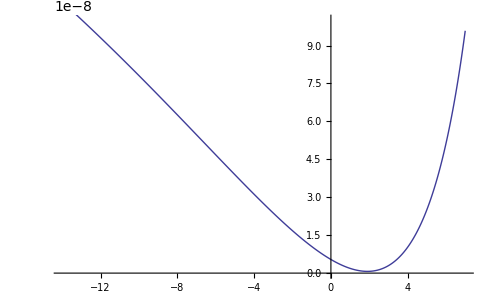

```mathematica
(*Graph d vs. variance(d)*)
varValues=Table[{d,variance[d]},{d,-14,7,.01}];
ListPlot[varValues,Joined->True,PlotRange->{0,10^-7}]
```

{3.,2.95643×10^-9}

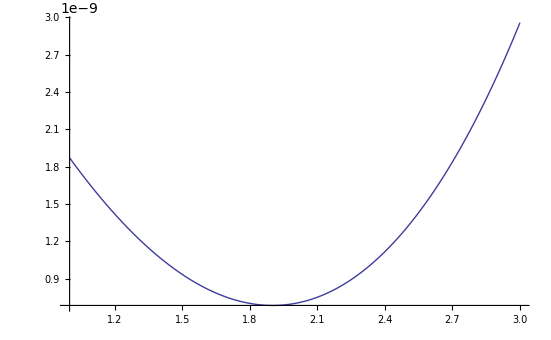

```mathematica
(*Graph d vs. variance(d)*)
varValues=Table[{d,variance[d]},{d,1,3,.001}];
varValues⟦-1⟧
ListPlot[varValues,Joined->True]
```

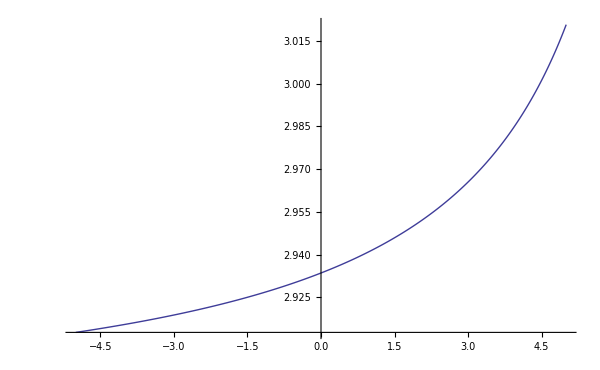

```mathematica
(*Graph d vs. a=upperbound*)
upperlimitValues=Table[{d,upperlimit[d]},{d,-5,5,.01}];
ListPlot[upperlimitValues,Joined->True]
```

1.9

FittedModel[2.9502-0.629977/(-1.9+x)^0.570942]

{a→2.9502,b→0.629977,c→0.570942}

{2.9502-0.629977/(-1.9+x)^0.570942,{0.000036066,-0.0000773036,0.0000426917,-0.0000310409,0.000036832,-0.0000282977,0.0000316027,-0.0000194067,0.0000312903,-0.0000159012,0.000023514,-0.0000176541,0.000010598,-0.000015521,8.53386×10^-6,-0.000016669,6.06873×10^-6,-0.0000142542,4.90762×10^-6,-0.0000123199,5.24568×10^-6,-8.3502×10^-6,7.58877×10^-6,-2.43102×10^-6,0.0000112766,2.93358×10^-6}, | Estimate | Standard Error | t-Statistic | P-Value
a | 2.9502 | 0.000265289 | 11120.7 | 6.53379×10^-79
b | 0.629977 | 0.000952053 | 661.704 | 1.00164×10^-50
c | 0.570942 | 0.0012903 | 442.486 | 1.04704×10^-46}

6.84329×10^-10

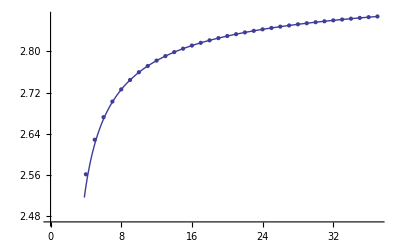

```mathematica
(*minimum variance*)
d=1.900
nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b ((x-d )^(-c)),{a,b,c},x]
nlm["BestFitParameters"]
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}]
Total[g^2]/(Length[g]-1)
Show[ListPlot[norms],Plot[f,{x,0,37}]]
```

4.466

FittedModel[3.00002-0.436373/(-4.466+x)^0.342838]

{a→3.00002,b→0.436373,c→0.342838}

{3.00002-0.436373/(-4.466+x)^0.342838,{0.000343008,-0.0000760081,-0.0000947412,-0.000214101,-0.000140805,-0.000174036,-0.000070344,-0.0000743658,0.0000213668,0.0000142878,0.0000872708,0.0000723469,0.000119265,0.000104301,0.000132264,0.000104094,0.000117424,0.0000817055,0.0000799437,0.0000367104,0.0000236154,-0.0000248926,-0.0000477403,-0.000100071,-0.000131873,-0.000188627}, | Estimate | Standard Error | t-Statistic | P-Value
a | 3.00002 | 0.00258749 | 1159.43 | 2.50319×10^-56
b | 0.436373 | 0.000600807 | 726.311 | 1.17543×10^-51
c | 0.342838 | 0.00526936 | 65.0626 | 1.39195×10^-27}

1.60171×10^-8

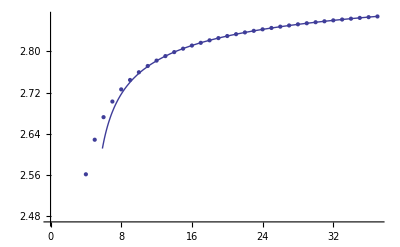

```mathematica
(*intersection with x axis for F to be amenable*)
d=4.466
nlm=NonlinearModelFit[norms⟦Range[12,Ntuple]⟧,a-b ((x-d )^(-c)),{a,b,c},x]
nlm["BestFitParameters"]
{f,g,h}=nlm[{"BestFit","FitResiduals","ParameterTable"}]
Total[g^2]/(Length[g]-1)
Show[ListPlot[norms],Plot[f,{x,0,37}]]
```